```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es4_coseno_iperbolico\\data_trapezio.txt","Table"];
Trapezio = Take[data][[All,{1,3}]];
DELTATrapezio = Take[data,-500][[All,{2,4}]];
```

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es4_coseno_iperbolico\\data_simpson.txt","Table"];
Simpson= Take[data][[All,{1,3}]];
DELTASimpson= Take[data,-250][[All,{2,4}]];
```

```mathematica
data= Import["E:\\Alessio\\Desktop\\Computazionale\\es4_coseno_iperbolico\\data_legendre.txt","Table"];
DELTALegendre = Take[data][[All,{1,3}]];
```

```mathematica
data = Import["E:\\Alessio\\Desktop\\Computazionale\\es4_coseno_iperbolico\\data_laguerre.txt","Table"];
DELTALaguerre= Take[data][[All,{1,3}]];
```

```mathematica
data =Import["E:\\Alessio\\Desktop\\Computazionale\\es4_coseno_iperbolico\\data_romberg.txt","Table"];
Romberg1 = Take[data,{8,20}][[All,{1,2}]];
Romberg2 = Take[data,{7,13}][[All,{1,3}]];
Romberg3 = Take[data,{3,10}][[All,{1,4}]];
```

```mathematica
model = a*x^b  ;
```

```mathematica
linetrap=FindFit[DELTATrapezio, model,{a,b},x]
```

{a→3321.7,b→2.01198}

```mathematica
linesimp=FindFit[DELTASimpson, model,{a,b},x]
```

{a→6154.24877586726993310495539387016621287783,b→4.03055484256707008834927931497346052008769}

```mathematica
lineromb1=FindFit[Romberg1, model,{a,b},x]
lineromb2=FindFit[Romberg2, model,{a,b},x]
lineromb3=FindFit[Romberg3, model,{a,b},x]
```

{a→3297.01187741794497327977841987302214360118,b→2.01052944985684335754286677929878314759049}

{a→6570.10930562977428198087735152610276942,b→4.04410038036786021050569433144953008942}

{a→148575.5593559493249344664714245191285,b→6.271429698653579568489843230290545868}

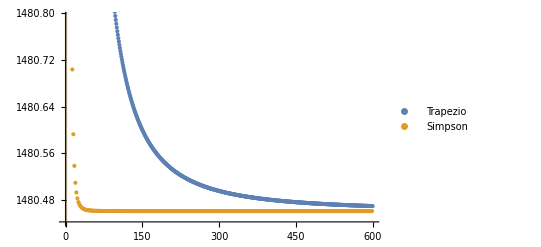

```mathematica
Show[{ListPlot[{Trapezio,Simpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->Automatic],Plot[{model/.linetrap,model/.linesimp},{x,0,1},PlotStyle->Opacity[0.4]]}]
```

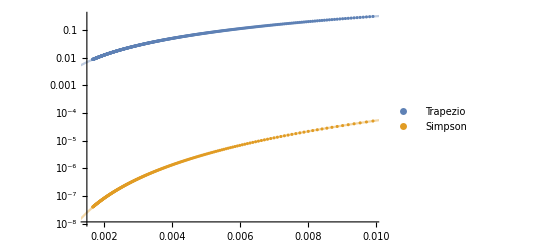

```mathematica
Show[{ListLogPlot[{DELTATrapezio,DELTASimpson}, PlotLegends->{"Trapezio", "Simpson"},PlotRange->All],LogPlot[{model/.linetrap,model/.linesimp},{x,0,0.02},PlotStyle->Opacity[0.4]]}]
```

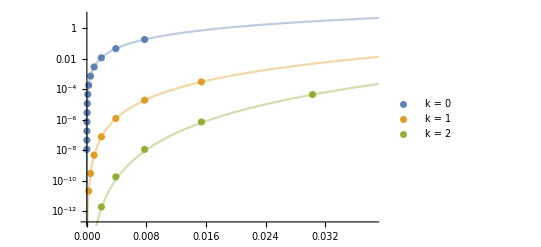

```mathematica
Show[{ListLogPlot[{Romberg1,Romberg2,Romberg3},PlotLegends->{"k = 0","k = 1","k = 2"},PlotRange->Automatic],LogPlot[{model/.lineromb1,model/.lineromb2,model/.lineromb3},{x,0,0.05},PlotStyle->Opacity[0.4]]}]
```

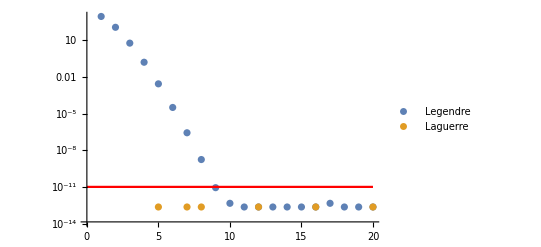

```mathematica
Show[{ListLogPlot[{DELTALegendre, DELTALaguerre}, PlotLegends->{"Legendre", "Laguerre"}, PlotRange->{{0,20},Automatic}],LogPlot[10^(-11),{x,0,20},PlotStyle->Red]}]
```

```mathematica
g[x_]= Cosh[x]
```

Cosh[x]

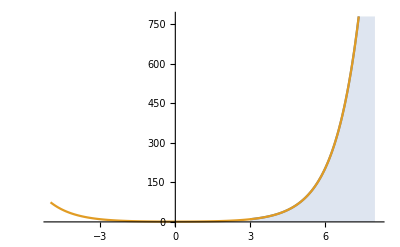

```mathematica
Plot[{If[3<x<8, g[x]],g[x]},{x,-5,8.1}, Filling->{1->Axis}]
```

```mathematica
Integrate[g[x],{x,3,8}]
N[%]
```

-Sinh[3]+Sinh[8]

1480.46

```mathematica
f[y_]:=NIntegrate[g[x],{x,2,y}]
```

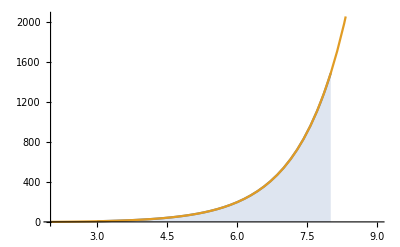

```mathematica
Plot[{If[3<x<8, f[x]],f[x]},{x,2,9}, Filling->{1->Axis}]
```